# Fourier and Fouriest

## Explorations in alternative base representations

Edridge D’Souza Final Project
Honors 391H with Prof. Manes, Spring 2018

## Introduction

I started this class with some basic experience in Mathematica (mainly for its plotting capabilities), which I use in my research in the Biochemistry department. As someone who cares about the applied side of mathematics, much of the number theory in this class came as new information to me. Without much formal training in number theory, I became interested in how to use Mathematica to compute things that may not be obvious by hand.

As I was searching for ideas for this project, I came upon a strip from the web comic Saturday Morning Breakfast Cereal.

-Graphics-(source)^[1]
It seems like a fairly ridiculous idea. A play on the idea of a “Fourier transform” to relate to alternative base representations. However, this is an area where Mathematica can really shine, as it’s possible to rapidly convert numbers to alternative base representations. Perhaps, then, Mathematica can allow us to compute 4ier and 4iest transforms of numbers. Once we do this, what interesting patterns may we find? Will there be any patterns at all? Some people on the Internet have already done analyses involving the 4ier and 4iest numbers^[2,3,4], but the aim of this project is to extend that and to find patterns.

I don’t have the formal math background to understand all of the reasons behind the patterns I find. However, I’m experienced in data visualization and statistical modeling, so my approach seeks to use data visualization to find patterns. From there, these patterns can theoretically be interpreted from a more number theoretic perspective.

## Background and Goals

### Prototyping the 4ier Transforms

Mathematica natively comes with the function BaseForm[], which allows conversion to other bases.

```mathematica
?BaseForm
```

BaseForm[expr,n] prints with the numbers in expr given in base n.

By creating expressions to convert the first k numbers (for sufficiently large k) to different bases, we might be able to find 4ier and 4iest transforms for the first k numbers. The easiest and most generalizable way to count the occurrence of the digit 4 in the resultant representation is to use Mathematica’s string processing capabilities. The function ToString[] can convert the alternate-base representation to a searchable string, and the function StringCount[] can search for occurrences of the digit 4 within the resultant string.

```mathematica
?ToString
```

ToString[expr] gives a string corresponding to the printed form of expr in OutputForm. 
ToString[expr,form] gives the string corresponding to output in the specified form.

```mathematica
?StringCount
```

StringCount[string,sub] gives a count of the number of times "sub" appears as a substring of "string". 
StringCount[string,patt] gives the number of substrings in "string" that match the general string expression patt. 
StringCount[string,{patt_1,patt_2,…}] counts the number of occurrences of any of the patt_i. 
StringCount[{s_1,s_2,…},p] gives the list of results for each of the s_i.

The BaseForm[] function contains the limitation that it can only convert numbers from base 2 to base 36. If this prototyping is successful, we can develop a new base representation function that can covert to more bases. We can potentially do this using ASCII characters to represent unique digits. We can use a base-conversion algorithm to convert our base-10 numbers to alternative forms. In imperative Python-style pseudocode style, we can define an algorithm^[5] for such a conversion. This is based on the theory of alternate base systems^[6], in which for a base-b system, the digit d in the n-th position of the number (starting from the right) will be d*b^(n-1).

function ConvertBases (decimalNum, newBase) :
  	result = ""
	while decimalNum != 0 :
 		quotient, remainder = DivideWithRemainder (decimalNum, newBase)
		result = string (remainder) + result
		decimalNum = quotient
	return integer (result)

Such an extension will be necessary only once we have already gotten some results for bases 2 through 36. Once we have done this as a proof of concept, we can generalize to higher bases and repeat our analysis. For now, we will focus on gathering data just for bases 2 through 36.

Once we have established 4ier and 4iest transforms for the first k numbers, we can use Mathematica's plotting capabilities to visualize and determine the relationship, if any, between the number we test and the number of 4's in its 4iest transform. We can also try to determine a relationship between the number and the base b of its 4iest transform.

### Extension: The N-ier and N-iest transforms

Generalizing the 4ier and 4iest transforms to other bases, we can find the N-ier and N-iest transforms, for N from 1 to 35. Again, as with the 4ier and 4iest transforms, once we have prototyped all of these goals, we can repeat them with higher bases and explore more patterns. For now, we should focus on simply getting results from Mathematica’s native BaseForm[] function.

For each number from 1 to k, for arbitrarily large k, we will compute change-of-base for bases 2 through 36, and then find which base will provide the Nier and Niest transforms for N from 1 through 35. Once this is computed, we can do similar visualization methods as before. For each number N, we can graphically determine a relationship between the number being converted and the number of occurrences of N in its Niest transform. We can also see the relationship between the number and the base b of its Niest transform

### Benford’s Law

Benford’s Law is based on an observation that the first digits of certain sequences are not uniformly distributed from 1 to 9, and that rather, the number 1 seems to be significantly more common^[7]. This law was first observed in the days of logarithm tables, when Simon Newcomb noticed that the pages corresponding to the logarithms starting with 1 were more worn, and therefore more common, than logarithms starting with any other digit. If the first digit of base-n logarithms were evenly distributed, we might expect that the first digit d would be uniformly distributed such that d \[Distributed] Uni(1, n-1). 

However, in a base-b representation of a sequence known to follow Benford’s Law, the actual probability distribution of a given digit d being the first digit for a number in the sequence will be given by:

P(d) = log_b(1 + 1/d).

Certain sequences are known to follow Benford’s Law, including the Fibonacci Sequence, the powers of 2, and the factorials^[8,9].  The objective of this section of the project will be to convert each of these sequences from base 2 through base 36 using Mathematica's BaseForm[] function, and then use Mathematica's plotting capabilities to visualize how these sequences follow Benford's Law in other bases. Future extensions include visualizing Benford's Law for higher bases, using our custom base-conversion function.

## The 4ier and 4iest Transforms

First, we should define a procedure for converting a number to base N, for N from 2 to 36, and counting the number of occurrences of the digit 4 in each of the representations. Vectorized code will be attempted, but for certain tasks, modular imperative code will be simplest.

First, we will make a function that represents a given number in all the bases from 2 to 36. Then we will convert the representation to a string, and extract only the digits (ignoring the string representation of the base. Finally, we will package the results in a data structure of nested lists. Each element will represent a base (the first sub-element) and a list of its representations in base 2 through 36 (the second sub-element). Testing this on a small number, we can see the form that the results take.

```mathematica
Clear[ConvertToBase2Through36]
Clear[BaseConversionTable]
ConvertToBase2Through36[num_Integer]:=
Module[{N, representations, representationStrings, getOnlyDigits, lastDigitPos},
representations = Table[BaseForm[num,N], {N,2,Min[36, num+1]}]; (*No use representing in a base greater than or equal to the number*)
representationStrings = Map[ToString,representations];
getOnlyDigits:= Function[{string}, (*Take everything before the newline symbol*)
lastDigitPos = StringPosition[string,"\n"][[1]][[1]]-1 // Quiet;
If[lastDigitPos=={},lastDigitPos=StringLength[string],lastDigitPos=lastDigitPos]; (*Some strings don't have the subscript so we won't find a position of the newline character*)
StringTake[string, lastDigitPos]
]; 
Map[getOnlyDigits,representationStrings]
]
BaseConversionTable[start_Integer,k_Integer]:=Table[{i,ConvertToBase2Through36[i]},{i,start,k}]
BaseConversionTable[1,10]
```

{{1,{1}},{2,{10,2}},{3,{11,10,3}},{4,{100,11,10,4}},{5,{101,12,11,10,5}},{6,{110,20,12,11,10,6}},{7,{111,21,13,12,11,10,7}},{8,{1000,22,20,13,12,11,10,8}},{9,{1001,100,21,14,13,12,11,10,9}},{10,{1010,101,22,20,14,13,12,11,10,a}}}

We can now design a function that takes the results of BaseConversionTable[] and then determines which positions are 4ier and which are 4iest.

```mathematica
Clear[FourierSearch]
Clear[FindFouriers]
FourierSearch[base10_Integer, representations_List]:=Module[{CountFours, baseTenFourCount, listFourCount, bases,representationsAndFourCount, fouriers},
CountFours = Function[{num},StringCount[ToString[num],"4"]];
baseTenFourCount = CountFours[base10];
listFourCount = Map[CountFours, representations];
bases=Table[i,{i,2,Length[representations]+1}];
representationsAndFourCount = Transpose[{representations, bases,listFourCount}];
fouriers = Select[representationsAndFourCount, 
Function[{tuple}, 
If[baseTenFourCount>0,
tuple[[3]] >= baseTenFourCount, 
tuple[[3]] > baseTenFourCount]
]
];
If[Length[fouriers]>0,
{base10, fouriers},
Unevaluated[Sequence[]]
]
(* Return the base10 number, then a list containing ordered triples of 4ier representations. Each triple is in the form of: {alternate representation, base, number of 4's}. If no 4ier representation, return nothing. *)
]
FindFouriers[start_Integer,k_Integer]:=Module[{tbl, str}, 
tbl=BaseConversionTable[start,k]; 
Table[
FourierSearch[tbl[[i-start+1]][[1]], tbl[[i-start+1]][[2]]], 
{i,start,start+Length[tbl]-1}
]
]
```

FindFouriers[] will take a maximum number k, and try to find 4ier transforms for each number from 1 to k. Then, it will create nested lists. At the first level, an element will contain the number being tested, and a list of its fourier transforms. Each 4ier transform is in the form of the tuple returned from FourierSearch[].

Now that we’ve defined FindFouriers[], it is trivial to define FindFouriest[]. We simply take the output of FindFouriers[] and select the tuple whose third value, corresponding to the number of 4’s, is highest. If a number doesn’t have a 4iest transform, we don’t return anything. If a number has multiple 4iest transforms, we return them all.

```mathematica
Clear[FindFouriest]
FindFouriest[fourierTable_List]:=Module[{},
Table[
{
fourierTable[[i]][[1]], 
If[
Length[fourierTable[[i]][[2]]]≠0,
Take[#,Ordering[Last/@#,-1]]&@fourierTable[[i]][[2]], (* https://stackoverflow.com/a/6666082 *)
{}
] 
},
{i, 1, Length[fourierTable]}]
]
```

We can see these functions in action for a small k = 20.

```mathematica
FindFouriers[1,20]
```

{{4,{{4,5,1}}},{9,{{14,5,1}}},{10,{{14,6,1}}},{11,{{14,7,1}}},{12,{{14,8,1}}},{13,{{14,9,1}}},{14,{{24,5,1},{14,10,1}}},{15,{{14,11,1}}},{16,{{24,6,1},{14,12,1}}},{17,{{14,13,1}}},{18,{{24,7,1},{14,14,1}}},{19,{{34,5,1},{14,15,1}}},{20,{{40,5,1},{24,8,1},{14,16,1}}}}

```mathematica
FindFouriest[FindFouriers[1,20]]
```

{{4,{{4,5,1}}},{9,{{14,5,1}}},{10,{{14,6,1}}},{11,{{14,7,1}}},{12,{{14,8,1}}},{13,{{14,9,1}}},{14,{{14,10,1}}},{15,{{14,11,1}}},{16,{{14,12,1}}},{17,{{14,13,1}}},{18,{{14,14,1}}},{19,{{14,15,1}}},{20,{{14,16,1}}}}

Now that our functions are working, we should decide on a sufficiently large value of k for which to try our analysis on. Let’s see how the timing of this operation changes with successively larger values of k. We will use exponentially increasing values of k and fit a linear model to estimate the approximate value of k to use in order to maximize 1.5 hours (5400 seconds) of computation.

```mathematica
testvalues = {1,10,100,1000,10000,100000};
timingTitration = Transpose[{Table[i, {i,testvalues}],
Table[Timing[FindFouriest[FindFouriers[1,i]]][[1]],{i,testvalues}]}];
timingTitration//TableForm

timingModel = LinearModelFit[timingTitration,x,x];
timingModel["RSquared"]
timingModel["BestFit"]
Solve[timingModel["BestFit"]==5400,x]
```

1 | 0.
10 | 0.004
100 | 0.064
1000 | 0.672
10000 | 6.716
100000 | 70.24

0.999981

-0.0657512+0.000702815 x

{{x→7.68348×10^6}}

According to this regression, whose fit and R^2 are displayed above, we can get about 1.5 hours of computation if we set k to between 6 and 8 million. Now, I attempted to calculate this, but after about 15-20 minutes, my program would invariably start crashing: too many results were stored in memory, and my computer would run out of RAM. Therefore, we can find a limit for k that will take around 15-20 minutes to solve.

```mathematica
Solve[timingModel["BestFit"]==15*60,x]
```

{{x→1.28066×10^6}}

According to this regression, a value of k = 1,000,000 will give us approximately 15 minutes of computational time. From the timing model above, it seems that this is approximately O(n) in terms of time, so if we want to do this for larger values of k, we simply need more RAM to hold the results. Calculating the first million numbers’ 4ier transforms gives us these results.

```mathematica
firstMillionFouriers = Timing[FindFouriers[1,1000000]];
Print["Computed first million 4iers. Timing: ",firstMillionFouriers[[1]], " seconds (", N[firstMillionFouriers[[1]]/(60), 4], " minutes)"]
firstMillionFouriers = firstMillionFouriers[[2]];
Save[NotebookDirectory[]~~"fouriers.wl",
 firstMillionFouriers];
Clear[firstMillionFouriers]
```

Computer first million 4iers. Timing: 761.524 seconds (12.6921 minutes)

Now that this is computed, we can retrieve it later without rerunning this expensive computation.

```mathematica
firstMillionFouriers = Get[NotebookDirectory[]~~"fouriers.wl"];
firstMillionFouriests = Timing[FindFouriest[firstMillionFouriers]];
Print["Computed first million 4iests. Timing: ",firstMillionFouriests[[1]], " seconds (", N[firstMillionFouriests[[1]]/(60), 4], " minutes)"]
firstMillionFouriests = firstMillionFouriests[[2]];
Save[NotebookDirectory[]~~"fouriests.wl",
 firstMillionFouriests]
Clear[firstMillionFouriests]
```

Computed first million 4iests. Timing: 65.08 seconds (1.08467 minutes)

### Pattern Visualization of 4ier and 4iest

Now that we’ve gathered the data, we can clear all of the user-defined items in the global namespace, and load only the datasets we’re working on for visualization.

```mathematica
ClearAll["Global`*"]
```

#### 4ier Visualizations

```mathematica
firstMillionFouriers = Get[NotebookDirectory[] ~~ "fouriers.wl"];
```

For a representative example, we can look at the 500,000th element in the list of 4ier representations.

```mathematica
firstMillionFouriers[[500000]]
```

{500014,{{112000024,5,1},{14414514,6,4},{4151524,7,2},{1720456,8,1},{841801,9,1},{500014,10,1},{20143a,12,1},{146788,13,1},{d0314,14,1},{9d244,15,2},{4dd4a,18,2},{2bkh4,21,1},{1i24h,23,1},{1c41m,24,1},{ifh4,30,1},{du4v,33,1},{bn64,35,1}}}

Now that we see the structure of each element in the list of 4iers, we can graph the number (in base 10) against the number of 4ier representations it has.

```mathematica
ListLogLinearPlot[
Transpose[
{
Table[firstMillionFouriers[[i]][[1]],{i,1,Length[firstMillionFouriers]}],
Table[Length[firstMillionFouriers[[i]][[2]]],{i,1,Length[firstMillionFouriers]}]
}
],
AxesLabel->{"Number","Number of 4ier representations"},
PlotLabel->"Number of 4ier representations, by number"
] // Timing
```

{37.92,-Graphics-}

These results make sense, because as the numbers get bigger, there are more ways to potentially represent them.
Next, we can explore the relationship between the final digit of each number in its base 10 form, and the number of 4ier representations it has.

{307.92,Null}

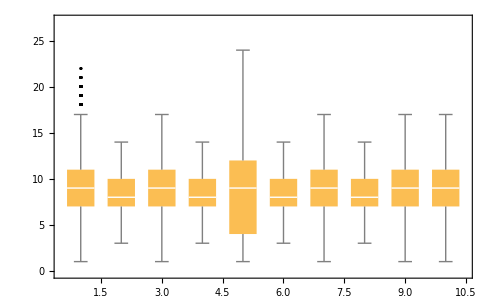

```mathematica
lastDigits = Table[{},{i, 1,10}];
Do[Module[{currentLastDigit, currentList},
currentLastDigit = Mod[firstMillionFouriers[[i]][[1]],10] + 1;(*Of course Mathematica has 1-based indexing, so the first element corresponds to numbers ending in 0*)
currentList = Append[lastDigits[[currentLastDigit]], 
Length[firstMillionFouriers[[i]][[2]]]];
lastDigits[[currentLastDigit]] = currentList;
],
{i,1,Length[firstMillionFouriers]}] //Timing
BoxWhiskerChart[lastDigits, "Outliers",ChartLabels->{0,1,2,3,4,5,6,7,8,9,10}, 
FrameLabel->{"Final digit","Number of 4ier representations"},
PlotLabel->"Number of 4ier representations, by final digit"]
```

It looks like there is a much higher variability when the final digit of the number is 4. Furthermore, it looks like the means are slightly higher for even numbers, which are numbers that are more likely to be divisible by 4.

Now, we can try to represent the numbers in matrix form, so we can see in heatmap form what the densities are. We won’t plot all of the first million 4ier numbers, but only what will conveniently fit in this space.

0.204

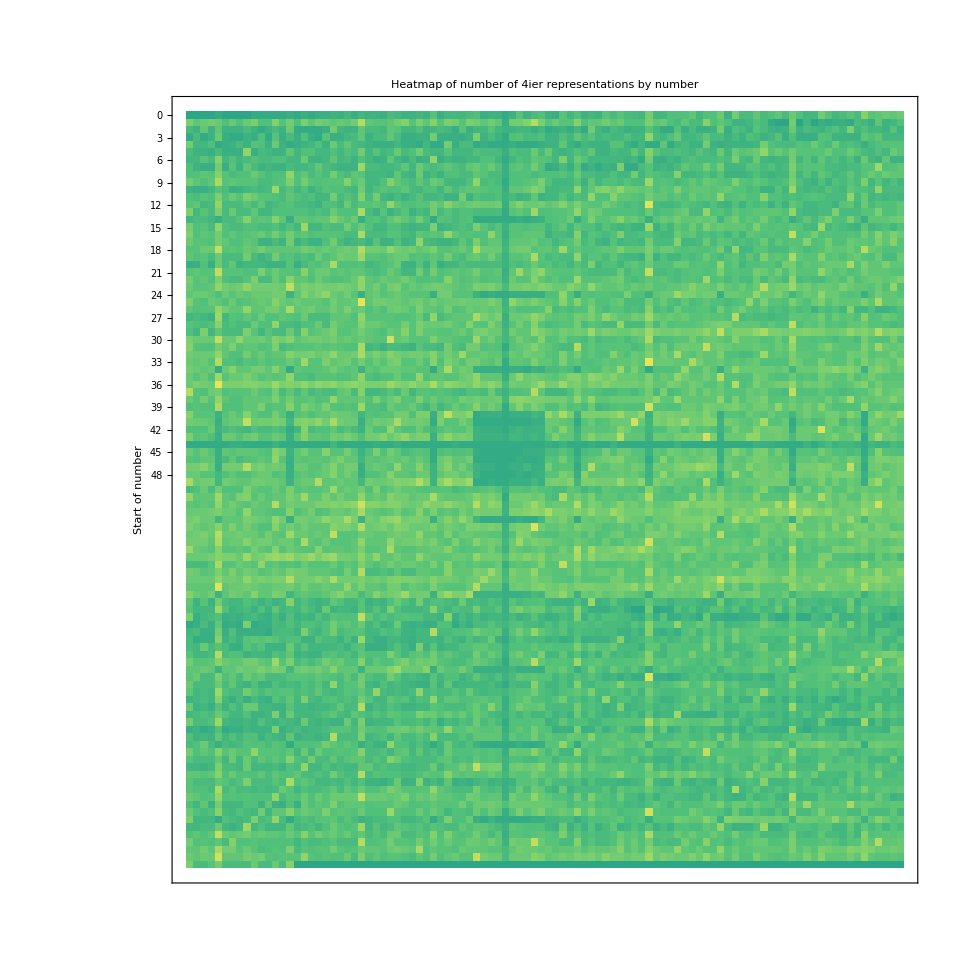

```mathematica
MakeHeatmap[width_Integer, total_Integer]:=Module[{},
matrix = Table[Table[0,{j,1,width}],{i,QuotientRemainder[firstMillionFouriers[[total,1]],width][[1]]+1}];
Do[Module[{num, quotientRemainder, col, row, numFouriers},
num = firstMillionFouriers[[i]][[1]];
quotientRemainder = QuotientRemainder[num,width];
col = quotientRemainder[[2]];
row = quotientRemainder[[1]];
numFouriers = Length[firstMillionFouriers[[i]][[2]]];
"Print[num, " ", row, " ", col, " ", numFouriers];";
matrix[[row+1 ,col+1]] = numFouriers
],{i,1,total}];
MatrixPlot[matrix,
PlotLabel->"Heatmap of number of 4ier representations by number",
FrameTicks->{
Transpose[{Table[i,{i,1,QuotientRemainder[total,width][[1]]+1}],Table[i,{i,0,QuotientRemainder[total,width][[1]]}]}], None,None,
Transpose[{Table[i,{i,1,width}],Table[i,{i,0,width-1}]}]
},
ColorFunction->"BlueGreenYellow",
FrameLabel->{"Start of number",None,None,"\n\n\nEnd of number"}
,
 ColorFunctionScaling->True]
]
hm = Timing[MakeHeatmap[100,10000] ];
hm[[1]]
hm[[2]]
```

From this heatmap, we see some really interesting patterns. With yellow representing high values, green representing medium, and blue representing low, we see some interesting trends in how the base-10 digit frequency affects the number of 4ier representations. For one, the clearest examples are that numbers that contain 4 already. For number in which the first two and last two digits contain the digit 4, there is a clear square of lower values, corresponding to numbers that don’t have many 4ier transforms, because they already have many 4’s in their base-10 representations. Interestingly, numbers ending in 04 appear to be more likely to have more 4ier representations. We also see a prominent diagonal line, going from the top right to the bottom left.

The results we see from this heatmap correlate well to what we’ve seen from the box-and-whiskers plot: that numbers ending in 4 tend to have a higher variability in terms of the number of 4ier transforms they have. There are spots of extreme increase and decrease relative to numbers ending in other digits. There are a few explanations for this phenomenon. First, for numbers that already have many 4’s in the base 10 representation, such as 4444 in the middle of the blue-green square, there are very few alternative base representations that would have as many or more 4’s. Therefore, two or more 4’s in a base 10 representation makes it very unlikely to find any 4ier representations. However, when there is only one 4 in the base 10 representation, we interestingly find a slight increase in the number of 4ier representations. This is due to how we’ve decided to count 4ier representations. If we look at the code, we realize that for a number with 1 or more 4’s, an alternate representation is considered 4ier if its number of 4’s is greater than or equal to the number of 4’s in base 10. However, if the number has zero 4’s, we don’t count any of the representations with zero 4’s to be equally 4ier, since a number cannot be 4ier than another number if it contains no 4’s. Thus, for a base 10 number, the shift from zero 4’s to one 4 will slightly increase the number of possible 4ier representations, but the shift from one 4 to two or more 4’s will drastically decrease it.

To illustrate this concept, we can make a boxplot of the number of 4’s in the original base 10 representation, as compared to the number of 4ier representations present. We see results similar to the pattern just described.

{1029.66,Null}

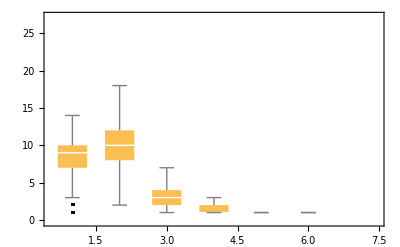

```mathematica
Clear[numberOfFours];
numberOfFours = Table[{},{i, 0,6}]; (*Handles all numbers from 1 to 1,000,000*)
Do[Module[{currentNumberOfFours,currentList },
currentNumberOfFours = StringCount[ToString[firstMillionFouriers[[i]][[1]]],"4"] + 1; (*Again, this +1 is due to 1-indexing*)
currentList = Append[numberOfFours[[currentNumberOfFours]], 
Length[firstMillionFouriers[[i]][[2]]]];
numberOfFours[[currentNumberOfFours]] = currentList;
],
{i,1,Length[firstMillionFouriers]}] //Timing
BoxWhiskerChart[numberOfFours, "Outliers",ChartLabels->{0,1,2,3,4,5,6}, 
FrameLabel->{"Number of 4s in base 10","Number of 4ier representations"},
PlotLabel->"Number of 4ier representations by number of 4s in base 10"]
```

This is consistent with our observation. The transition from zero to one 4 represents a modest increase, and any additional 4s after that will drastically decrease the number of available 4ier representations. Now that we have completed these exploratory analyses of the 4ier numbers, we can proceed to the 4iest numbers. Once again, we clear the global namespace so that we only load what we need, and then load our Fouriest dataset, before proceeding to our analysis.

#### 4iest visualizations

```mathematica
ClearAll["Global`*"]
firstMillionFouriests = Get[NotebookDirectory[] ~~ "fouriests.wl"];
```

For our first plot, we’ll simply compare the number against the base of its 4iest representation.

```mathematica
ListLogLinearPlot[
Transpose[
{
Table[firstMillionFouriests[[i]][[1]],{i,1,Length[firstMillionFouriests]}],
Table[firstMillionFouriests[[i,2,1,2]],{i,1,Length[firstMillionFouriests]}]
}
],
AxesLabel->{"Number","Base of 4iest representation"},
PlotLabel->"Base of 4iest representation, by number"
] // Timing
ListLogLinearPlot[
Transpose[
{
Table[firstMillionFouriests[[i]][[1]],{i,1,Length[firstMillionFouriests]}],
Table[firstMillionFouriests[[i,2,1,3]],{i,1,Length[firstMillionFouriests]}]
}
],
AxesLabel->{"Number","Number of 4s in 4iest representation"},
PlotLabel->"4s in 4iest representation, by number"
] // Timing
```

{23.344,-Graphics-}

```mathematica
{26.544,-Graphics-}
```

In these outputs, it is worth observing the upwards curves in the first plot. For the number 1 through 39, these curves correspond approximately to (n-4), indicating that the 4iest representation will generally be in the base that is 4 less than the number.  Because we only tested from bases 2 through 36, these upwards curves appear to start repeating once the y-value hits 36. Ostensibly, testing more base representations would allow for a more complete look. However, if this existing pattern held true, we would see that for any number n, one of its 4ier representations (if not its 4iest representation) would be in base (n-4). This makes sense, because in base (n-4), a number containing zero 4’s in base 10 can be represented as 14 in base (n-4), which is equal to 1*(n-4)^1 + 4*(n-4)^0 = n. For most numbers, this single 4 is the 4iest the number can get. As n gets larger, we see other curves corresponding to more complicated representations such as 114 or 140. However, in this first plot, the representation 14 in base (n-4) is the most salient example.

Now that we’ve examined this distribution, we can see which bases are most likely to product 4iest representations, and determine any present patterns.

{14.596,Null}

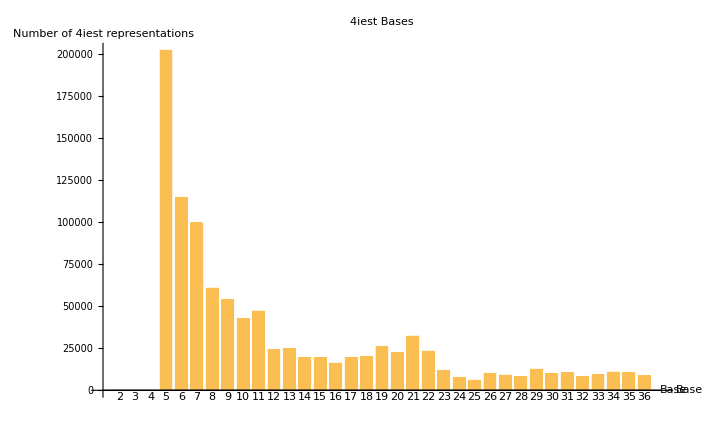

```mathematica
Clear[bases];
bases = Table[0,{i,2, 36}];
Do[Module[{currentListOfFouriests},
currentListOfFouriests = firstMillionFouriests[[i]][[2]];
Do[Module[{currentBase, currentBaseCount},
currentBase = currentListOfFouriests[[i]][[2]] - 1;
currentBaseCount = bases[[currentBase]] + 1;
bases[[currentBase]] = currentBaseCount;
],
{i,1,Length[currentListOfFouriests]}];
],
{i,1,Length[firstMillionFouriests]}
]//Timing
BarChart[bases,
 PlotLabel->"4iest Bases",
AxesLabel->{"Base","Number of 4iest representations"},
ChartLabels->Table[i,{i,2,36}]
]
```

It appears that base 5 is the base that is most likely to product a 4iest representation. This is understandable, since base 5 only contains the digits 0,1,2,3,4 and so we would expect the digit 4 to make up 1/5 of the digits of a base 5 number. Thus, we would expect the digit 4 to be much more frequent in base 5 than in higher bases. We can repeat this analysis by multiplying the number of 4iest representations by the base b, to account for the extra digits, to see if any bases tend to overrepresent the digit 4.

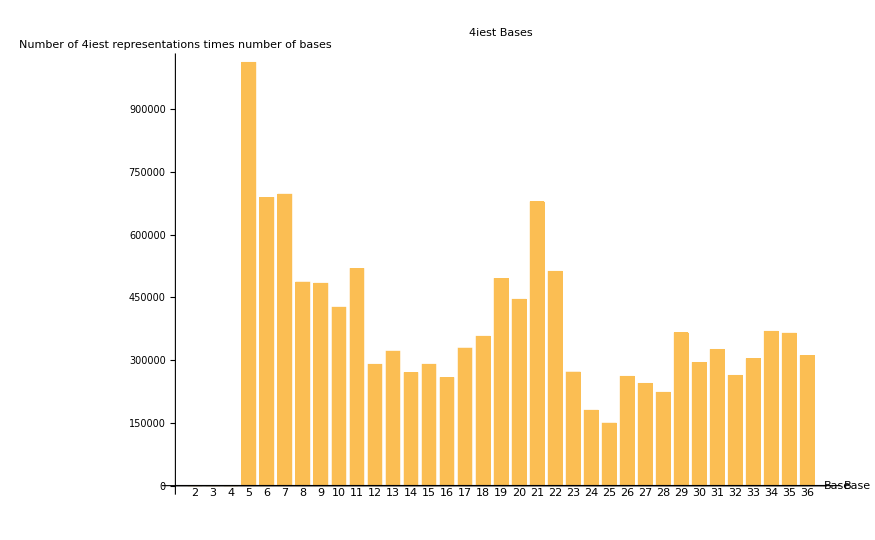
{0.104,-Graphics-}

```mathematica
BarChart[Table[bases[[base-1]]*base, {base,2,36}],
 PlotLabel->"4iest Bases",
AxesLabel->{"Base","Number of 4iest representations times number of bases"},
ChartLabels->Table[i,{i,2,36}]
]//Timing
```

We now see that there’s a slight peak at base 21. Base 5 is still the most frequent, but when we account for the fact that other bases have many possible digits, we see that the digit 4 tends to be more common than expected in bases 19 through 22. There may or may not be any significance to this, but it shows us interesting patterns about the 4iest representations.

This concludes our analysis of 4ier and 4iest numbers. We will repeat this analysis an another base, for n=5, to find the 5ier and 5iest numbers. In theory, it should be possible to repeat this analysis for all bases, but extending the analysis to base 5 will suffice as a proof of principle. Before doing anything else, we should first get an estimate of how long each of the existing 4ier and 4iest analyses took. Based on the timing data as of the time I wrote this:

Calculating first million 4iers: 761.524 seconds
Calculating first million 4iests: 65.08 seconds
Plot 1: 37.92 seconds
Plot 2: 307.92 seconds
Plot 3: 0.328 seconds
Plot 4: 1029.66 seconds
Plot 5: 23.344 seconds
Plot 6: 26.544 seconds
Plot 7: 14.596 seconds
Plot 8: 0.104 seconds
Total: 2267.02 seconds (37 minutes, 47 seconds)

We can thus expect any repeat to take approximately 40 minutes of computational time. We can now repeat the analysis to find the 5ier and 5iest numbers.

## Nier and Niest Analysis

We can write a code to take an arbitrary N, and repeat the 4ier/4iest analyses. For the sake of clarity, we will highlight only the 5ier and 5iest transforms, but if this works, then it will work for other bases too. Here, I’m essentially taking the previously-written code and refactoring it to take arbitrary numbers, not just 4.

```mathematica
ClearAll["Global`*"]
Clear[ConvertToBase2Through36]
Clear[BaseConversionTable]
ConvertToBase2Through36[num_Integer]:=
Module[{N, representations, representationStrings, getOnlyDigits, lastDigitPos},
representations = Table[BaseForm[num,N], {N,2,Min[36, num+1]}]; (*No use representing in a base greater than or equal to the number*)
representationStrings = Map[ToString,representations];
getOnlyDigits:= Function[{string}, (*Take everything before the newline symbol*)
lastDigitPos = StringPosition[string,"\n"][[1]][[1]]-1 // Quiet;
If[lastDigitPos=={},lastDigitPos=StringLength[string],lastDigitPos=lastDigitPos]; (*Some strings don't have the subscript so we won't find a position of the newline character*)
StringTake[string, lastDigitPos]
]; 
Map[getOnlyDigits,representationStrings]
]
BaseConversionTable[start_Integer,k_Integer]:=Table[{i,ConvertToBase2Through36[i]},{i,start,k}]


Clear[NierSearch]
Clear[FindNiers]
NierSearch[base10_Integer, representations_List, myN_Integer]:=Module[{CountNs, baseTenNCount, listNCount, bases,representationsAndNCount, niers},
CountNs = Function[{num},StringCount[ToString[num],ToString[myN]]];
baseTenNCount = CountNs[base10];
listNCount = Map[CountNs, representations];
bases=Table[i,{i,2,Length[representations]+1}];
representationsAndNCount = Transpose[{representations, bases,listNCount}];
niers = Select[representationsAndNCount, 
Function[{tuple}, 
If[baseTenNCount>0,
tuple[[3]] >= baseTenNCount, 
tuple[[3]] > baseTenNCount]
]
];
If[Length[niers]>0,
{base10, niers},
Unevaluated[Sequence[]]
]
]

FindNiers[start_Integer,k_Integer, myN_Integer]:=Module[{tbl, str}, 
tbl=BaseConversionTable[start,k]; 
Table[
NierSearch[tbl[[i-start+1]][[1]], tbl[[i-start+1]][[2]], myN], 
{i,start,start+Length[tbl]-1}
]
]

Clear[FindNiest]
FindNiest[nierTable_List]:=Module[{},
Table[
{
nierTable[[i]][[1]], 
If[
Length[nierTable[[i]][[2]]]≠0,
Take[#,Ordering[Last/@#,-1]]&@nierTable[[i]][[2]], (* https://stackoverflow.com/a/6666082 *)
{}
] 
},
{i, 1, Length[nierTable]}]
]

(*Now test it out with N=5 to see whether our data still fits its expected form*)
FindNiest[FindNiers[1,20, 5]]
```

{{5,{{5,6,1}}},{11,{{15,6,1}}},{12,{{15,7,1}}},{13,{{15,8,1}}},{14,{{15,9,1}}},{15,{{15,10,1}}},{16,{{15,11,1}}},{17,{{15,12,1}}},{18,{{15,13,1}}},{19,{{15,14,1}}},{20,{{15,15,1}}}}

```mathematica
Clear[firstMillionNiersFunc];
Clear[firstMillionNiestsFunc];
Clear[firstMillionNiers];
Clear[firstMillionNiests];

(*Dummy variables needed to properly save results within the proper scope*)
firstMillionNiers = {};
firstMillionNiests = {};

firstMillionNiersFunc[myN_Integer] := Module[{result},
result = Timing[FindNiers[1,1000000, myN]];
Print["Computed first million " ~~ToString[myN]~~"iers. Timing: ",result[[1]], " seconds (", N[result[[1]]/(60), 4], " minutes)"];
firstMillionNiers =  result[[2]];
Save[NotebookDirectory[]~~ToString[myN]~~"iers.wl",
 firstMillionNiers];
Clear[result];
Clear[firstMillionNiers];
]
firstMillionNiestsFunc[myN_Integer]:=Module[{niers,result},
niers = Get[NotebookDirectory[]~~ToString[myN]~~"iers.wl"];
result = Timing[FindNiest[niers]];
Print["Computed first million " ~~ToString[myN]~~"iests. Timing: ",result[[1]], " seconds (", N[result[[1]]/(60), 4], " minutes)"];
firstMillionNiests = result[[2]];
Save[NotebookDirectory[]~~ToString[myN]~~"iests.wl",
 firstMillionNiests];
Clear[result];
Clear[firstMillionNiers];
Clear[firstMillionNiests];
]
```

Now that we’ve defined these, let’s put them in action for N=5. Once this calculation is complete, we can design a new module that simply produces all of the output plots that we saw before.

```mathematica
firstMillionNiersFunc[5]
firstMillionNiestsFunc[5]
```

Computed first million 5iers. Timing: 768.992 seconds (12.8165 minutes)

Computed first million 5iests. Timing: 70.68 seconds (1.178 minutes)

Now that the first million 5iers and 5iests are computed, we will create one overarching module that simply outputs all of the expected plots, as well as their timings. Again, we recycle code from the 4ier prototyping. One function for the 5ier analysis, and one for the 5iest analysis.

```mathematica
Clear[makeNierPlots];
makeNierPlots[myN_Integer]:=Module[{plt1,lastDigits, timing2, plt2,MakeHeatmap, plt3, numberOfNs, timing4, plt4},
firstMillionNiers = Get[NotebookDirectory[]~~ToString[myN]~~"iers.wl"];
Module[{},
Print["Representative example of a " ~~ ToString[myN] ~~ "ier list: "];
firstMillionNiers[[500000]]//Print
];

(*Plot 1*)
plt1 = ListLogLinearPlot[
Transpose[
{
Table[firstMillionNiers[[i]][[1]],{i,1,Length[firstMillionNiers]}],
Table[Length[firstMillionNiers[[i]][[2]]],{i,1,Length[firstMillionNiers]}]
}
],
AxesLabel->{"Number","Number of "~~ToString[myN]~~"ier representations"},
PlotLabel->"Number of "~~ToString[myN]~~"ier representations, by number"
] // Timing ;

(*Plot 2*)
lastDigits = Table[{},{i, 1,10}];
timing2=Do[Module[{currentLastDigit, currentList,},
currentLastDigit = Mod[firstMillionNiers[[i]][[1]],10] + 1;(*Of course Mathematica has 1-based indexing, so the first element corresponds to numbers ending in 0*)
currentList = Append[lastDigits[[currentLastDigit]], 
Length[firstMillionNiers[[i]][[2]]]];
lastDigits[[currentLastDigit]] = currentList;
],
{i,1,Length[firstMillionNiers]}] //Timing;
plt2={timing2[[1]],BoxWhiskerChart[lastDigits, "Outliers",ChartLabels->{0,1,2,3,4,5,6,7,8,9,10}, 
FrameLabel->{"Final digit","Number of "~~ToString[myN]~~"ier representations"},
PlotLabel->"Number of "~~ToString[myN]~~"ier representations, by final digit"]};

(*Plot 3*)
MakeHeatmap[width_Integer, total_Integer]:=Module[{matrix},
matrix = Table[Table[0,{j,1,width}],{i,QuotientRemainder[firstMillionNiers[[total,1]],width][[1]]+1}];
Do[Module[{num, quotientRemainder, col, row, numNiers},
num = firstMillionNiers[[i]][[1]];
quotientRemainder = QuotientRemainder[num,width];
col = quotientRemainder[[2]];
row = quotientRemainder[[1]];
numNiers = Length[firstMillionNiers[[i]][[2]]];
matrix[[row+1 ,col+1]] = numNiers
],{i,1,total}];
MatrixPlot[matrix,
PlotLabel->"Heatmap of number of "~~ToString[myN]~~"ier representations by number",
FrameTicks->{
Transpose[{Table[i,{i,1,QuotientRemainder[total,width][[1]]+1}],Table[i,{i,0,QuotientRemainder[total,width][[1]]}]}], None,None,
Transpose[{Table[i,{i,1,width}],Table[i,{i,0,width-1}]}]
},
ColorFunction->"BlueGreenYellow",
FrameLabel->{"Start of number",None,None,"\n\n\nEnd of number"}
,
 ColorFunctionScaling->True]
];
plt3 = Timing[MakeHeatmap[100,10000] ];

(*Plot 4*)
numberOfNs = Table[{},{i, 0,6}]; (*Handles all numbers from 1 to 1,000,000*)
timing4=Do[Module[{currentNumberOfNs,currentList },
currentNumberOfNs = StringCount[ToString[firstMillionNiers[[i]][[1]]],ToString[myN]] + 1; (*Again, this +1 is due to 1-indexing*)
currentList = Append[numberOfNs[[currentNumberOfNs]], 
Length[firstMillionNiers[[i]][[2]]]];
numberOfNs[[currentNumberOfNs]] = currentList;
],
{i,1,Length[firstMillionNiers]}] //Timing;
plt4={timing4[[1]],BoxWhiskerChart[numberOfNs, "Outliers",ChartLabels->{0,1,2,3,4,5,6}, 
FrameLabel->{"Number of "~~ToString[myN]~~"s in base 10","Number of "~~ToString[myN]~~"ier representations"},
PlotLabel->"Number of "~~ToString[myN]~~"ier representations by number of "~~ToString[myN]~~"s in base 10"]};

Clear[firstMillionNiers];
(*Print all of them. https://mathematica.stackexchange.com/a/80232 *)
CellPrint@ExpressionCell[#,"Output"]&/@{plt1,plt2,plt3, plt4};
]
```

Representative example of a 5ier list:

{500031,{{14414543,6,1},{4151550,7,3},{500031,10,1},{311754,11,1},{201453,12,1},{9d256,15,1},{5gd3a,17,1},{4dd59,18,1},{1i25b,23,1},{du5f,33,1}}}

{37.308,-Graphics-}

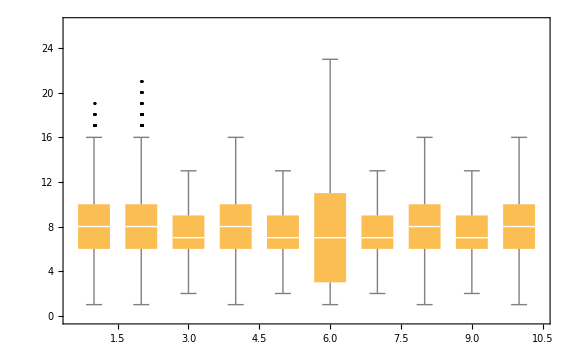
{293.644,-Graphics-}

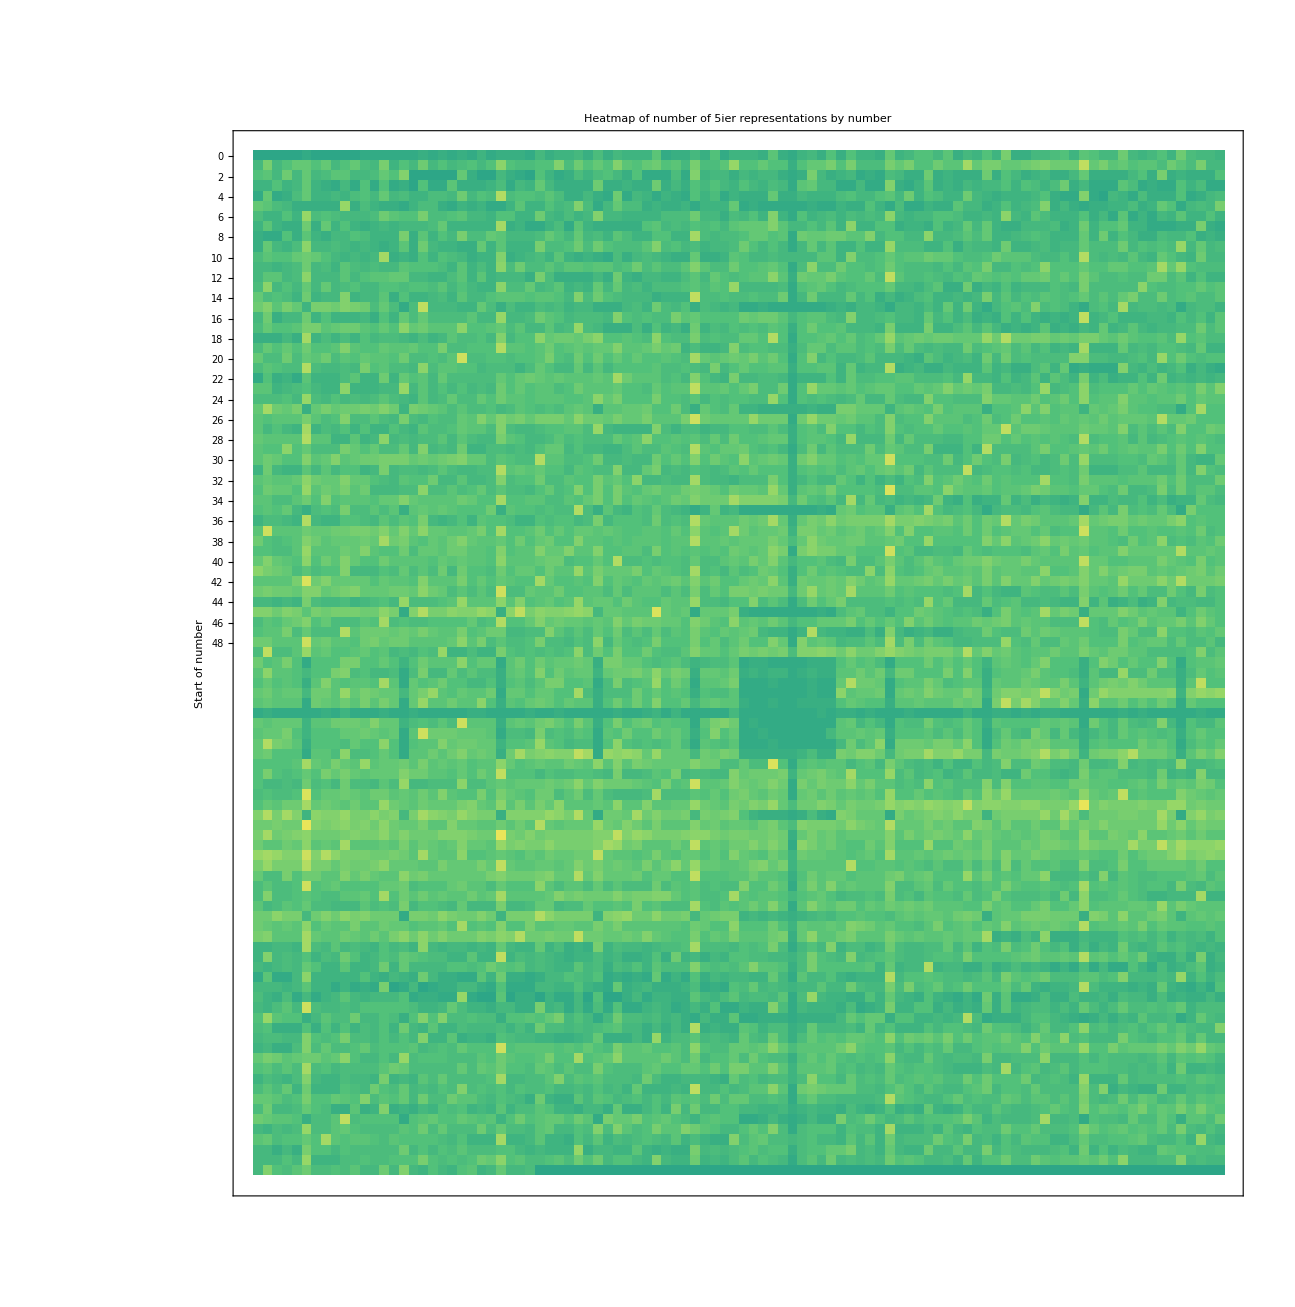
{0.232,-Graphics-}

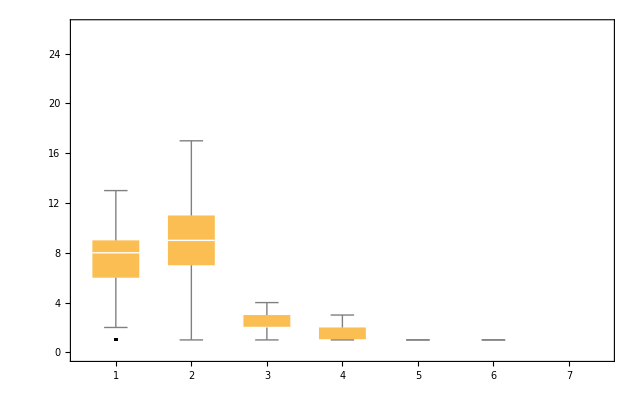
{1061.34,-Graphics-}

```mathematica
(*Now test it on N=5*)
makeNierPlots[5]
```

```mathematica
Clear[makeNiestPlots];
makeNiestPlots[myN_Integer]:=Module[{plt5, plt6, bases, timing7,plt7, plt8},
firstMillionNiests = Get[NotebookDirectory[]~~ToString[myN]~~"iers.wl"];

(*Plot 5*)
plt5 = ListLogLinearPlot[
Transpose[
{
Table[firstMillionNiests[[i]][[1]],{i,1,Length[firstMillionNiests]}],
Table[firstMillionNiests[[i,2,1,2]],{i,1,Length[firstMillionNiests]}]
}
],
AxesLabel->{"Number","Base of "~~ToString[myN]~~"iest representation"},
PlotLabel->"Base of "~~ToString[myN]~~"iest representation, by number",
PlotRange->All
] // Timing;

(*Plot 6*)
plt6 = ListLogLinearPlot[
Transpose[
{
Table[firstMillionNiests[[i]][[1]],{i,1,Length[firstMillionNiests]}],
Table[firstMillionNiests[[i,2,1,3]],{i,1,Length[firstMillionNiests]}]
}
],
AxesLabel->{"Number","Number of "~~ToString[myN]~~"s in "~~ToString[myN]~~"iest representation"},
PlotLabel->ToString[myN]~~"s in "~~ToString[myN]~~"iest representation, by number",
PlotRange->All
] // Timing;

(*Plot 7*)
bases = Table[0,{i,2, 36}];
timing7=Do[Module[{currentListOfNiests},
currentListOfNiests = firstMillionNiests[[i]][[2]];
Do[Module[{currentBase, currentBaseCount},
currentBase = currentListOfNiests[[i]][[2]] - 1;
currentBaseCount = bases[[currentBase]] + 1;
bases[[currentBase]] = currentBaseCount;
],
{i,1,Length[currentListOfNiests]}];
],
{i,1,Length[firstMillionNiests]}
]//Timing;
plt7 = {timing7[[1]],
BarChart[bases,
 PlotLabel->ToString[myN]~~"iest Bases",
AxesLabel->{"Base","Number of "~~ToString[myN]~~"iest representations"},
ChartLabels->Table[i,{i,2,36}]
]};

(*Plot 8*)
plt8 = BarChart[Table[bases[[base-1]]*base, {base,2,36}],
 PlotLabel->ToString[myN]~~"iest Bases",
AxesLabel->{"Base","Number of "~~ToString[myN]~~"iest representations times number of bases"},
ChartLabels->Table[i,{i,2,36}]
]//Timing;

Clear[firstMillionNiests];
CellPrint@ExpressionCell[#,"Output"]&/@{plt5,plt6,plt7, plt8};
]
```

{30.004,-Graphics-}

{28.592,-Graphics-}

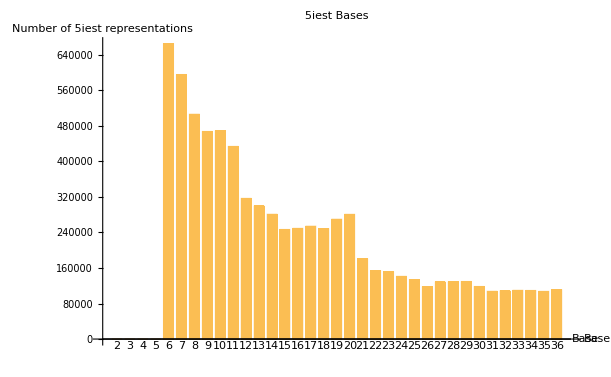
{63.104,-Graphics-}

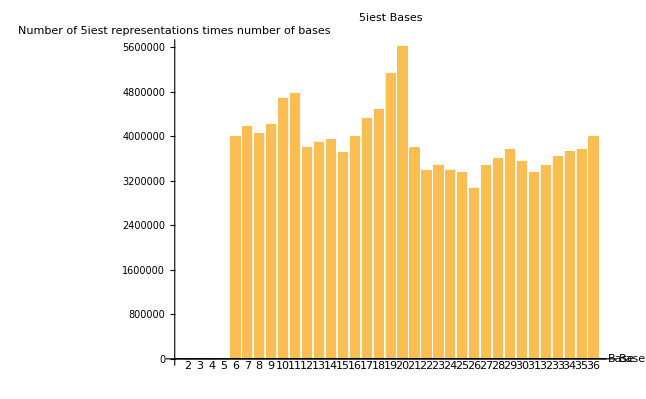
{0.128,-Graphics-}

```mathematica
(*Now test it out for N=5*)
makeNiestPlots[5]
```

This demonstrates that our pipeline can efficiently be run for arbitrary N. The total time it took to run for N=5 was 839.672 seconds to find the 5ier and 5iest numbers, 1392.524 seconds for the 5ier visualizations, and 121.828 seconds for the 5iest visualizations. The entire pipeline took 2354.024 seconds, or 39.234 minutes, consistent with what we saw for N=4. For all of the plots, we can interpret the results similarly to how we would interpret them for the N=4 prototype. Within this section, there is a total of 329 lines of code, and the code in this section is sufficient to be used as a reproducible pipeline for arbitrary N from 2 to 36. This effectively establishes a reproducible experimental pipeline for finding the Nier and Niest transforms, as well as generating these exploratory data visualizations.

## Benford’s Law

```mathematica
ClearAll["Global`*"]
```

We can test different sequences to see whether their first digits follow a Benford Distribution. To do this, we use Mathematica’s BenfordDistribution[] function, and set it to the base we are currently testing. We also use DistributionFitTest[], which performs a goodness-of-fit hypothesis test, with the null hypothesis that the observed data isn’t significantly different from the Benford Distribution. If we see that the hypothesis test has a p-value above a given α significance level (which I will conservatively set to 0.25), then we can fail to reject the null hypothesis, and declare that the observed digit distribution in a given base is consistent with the Benford Distribution.

Our function will take in a function that gives the i-th value of a sequence

```mathematica
?DistributionFitTest
?BenfordDistribution
```

DistributionFitTest[data] tests whether data is normally distributed. 
DistributionFitTest[data,dist] tests whether data is distributed according to dist. 
DistributionFitTest[data,dist,property] returns the value of "property".

BenfordDistribution[b] represents a Benford distribution with base parameter b.

```mathematica
Clear[BenfordTest];
BenfordTest[generatingFunction_Symbol, limits_List, base_Integer/; 2≤base≤36 , alpha_]:= Module[{firstDigits, digitFreqCount, currentDigit,currentDigitCount, xlabels,freqs,hyptest,message,reject, bar,theoretical, benf},
firstDigits = Table[StringTake[ToString[BaseForm[generatingFunction[i], base]], 1],
{i,limits[[1]],limits[[2]]}];
digitFreqCount = Table[0,{i,1,base-1}];
(*I don't know a more efficient way to do this. Set up a string to number conversion*)
Do[
currentDigit = Switch[firstDigits[[i]],
"1",1,"2",2,"3",3,"4",4,"5",5,"6",6,"7",7,"8",8,"9",9,"a",10,
"b",11,"c",12,"d",13,"e",14,"f",15,"g",16,"h",17,"i",18,"j",19,"k",20,
"l",21,"m",22,"n",23,"o",24,"p",25,"q",26,"r",27,"s",28,"t",29,"u",30,
"v",31,"w",32,"x",33,"y",34,"z",35
];
firstDigits[[i]] = currentDigit; (*Convert to numbers for use in hypothesis test*)
currentDigitCount = digitFreqCount[[currentDigit]] + 1;
digitFreqCount[[currentDigit]] = currentDigitCount,
{i,1,Length[firstDigits]}
];
xlabels =Table[{1,2,3,4,5,6,7,8,9,
"a","b","c","d","e","f","g","h",
"i","j","k","l","m","n","o","p",
"q","r","s","t","u","v","w","x","y","z"}[[i]],
{i,1,base-1}] ;
freqs = N@digitFreqCount/Total[digitFreqCount];

hyptest = DistributionFitTest[firstDigits, BenfordDistribution[base], "HypothesisTestData"];
(*Print[freqs];
Print[hyptest["PValue"]];*)
reject = (hyptest["PValue"] < alpha);
message = If[!reject,
ToString[✓],
ToString[☒]];

(*Bar chart of observed first-digit frequencies in a given sequence*)
bar =BarChart[freqs,
ChartLabels -> xlabels,
AxesLabel->{"Digit","Frequency"},
PlotRange->Automatic,
Epilog->{
Text[Style[message,45,
FontFamily->Times, 
FontColor->If[!reject,Green,Red]],
{Mean[{0,Length[digitFreqCount]}],Max[freqs]}
],
Text[Style[p = N[hyptest["PValue"],3],12, FontFamily->Times],
{Mean[{0,Length[digitFreqCount]}],Max[freqs]-0.05}]
},
PlotLabel->"Benford distribution in base "~~ToString[base]
];

(*Theoretical Benford distribution for a given base*)
theoretical=Table[PDF[BenfordDistribution[base],x],{x,1,base-1}];
benf=ListPlot[theoretical, PlotRange->{0,Max[theoretical]}, Filling->Axis];

(*Show them together*)
Show[bar,benf]
]
```

Now that we’ve declared this functionality, we can use Manipulate[] to test all of the bases from 2 through 36, to see whether the first digits of the first 1000 numbers follow a Benford distribution. The p-value is displayed below the check/x mark. In most cases, the p-value is close to 1, and is much higher than the α cutoff, indicating that the data is consistent with the null hypothesis that the data follows a Benford distribution. However, we will see that for certain bases, the data does not follow the Benford Distribution.

```mathematica
Manipulate[BenfordTest[Fibonacci, {1,1000}, base, 0.25],{base,2,36,1}]
```

Benford’s Law states that the Benford Distribution is the limit of the distribution of first digits, as we take more samples. Therefore, increasing the sample size where base=29 will show the distribution of digits more closely follow the Benford Distribution. As we increase our sample size, we see the data more closely resemble the predictions, and we find ourselves failing to reject the null hypothesis.

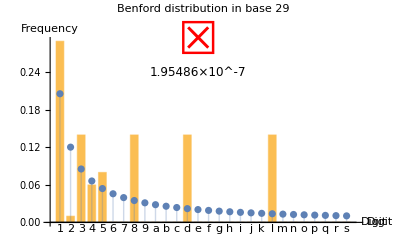
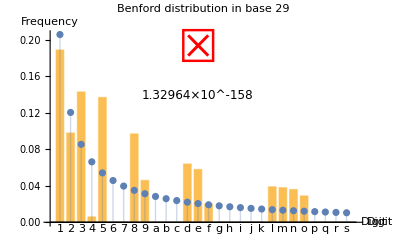
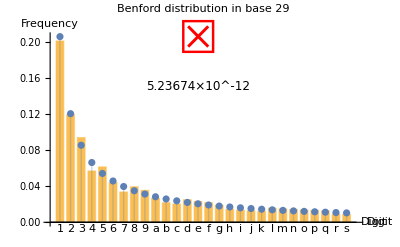
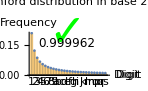

```mathematica
Table[BenfordTest[Fibonacci, {1,sampleSize}, 29, 0.25],
{sampleSize,{100,1000,10000,100000}}]
```

We therefore see that when the sample size is large enough, the first digits of the Fibonacci numbers will tend to follow a Benford distribution for bases 2 through 36. It is not clear why base 29 has an exception.

We can now try our analysis again with the powers of 2, another sequence known to follow Benford’s Law. By sampling the first 1,000 numbers of this sequence, we see that Benford’s Law is followed in all bases except for 4, 8, 16, and 32: bases that are powers of 2. We clearly see a relationship between the powers-of-2 sequence and the bases which don’t follow Benford’s Law at small sample sizes, which means that for the previous example, there may be some relationship between the Fibonacci sequence and the number 29.

```mathematica
PowersOfTwo[x_Integer]:=2^x
Manipulate[BenfordTest[PowersOfTwo, {1,1000}, base, 0.25],{base,2,36,1}]
```

Let’s try it on the factorials now! Sample size of 1,000. From what we see, the results generally tend to agree with Benford’s distribution if we use the more generous α value of 0.10, but the p-values tend to be much more variable than in the previous examples. Increased sample size would likely show us finding tighter alignment to the expected distribution.

```mathematica
Manipulate[BenfordTest[Factorial, {1,1000}, base, 0.10],{base,2,36,1}]
```

Finally, let’s test a distribution known not to follow Benford’s Law. One property that would make a sequence non-Benford would be if its digits were sequential. Therefore, we should expect that the sequence of the first 10,000 numbers or so would be non-Benford!

```mathematica
Manipulate[BenfordTest[Identity, {1,10000}, base, 0.25],{base,2,36,1}]
```

## Difficulties and Conclusions

### 4ier/4iest and Nier/Niest transforms

#### RAM and storage

It very quickly became apparent that calculating the 4ier and 4iest transforms for the first N numbers, for arbitrarily large N, quickly yielded problems. As demonstrated in the linear model fit, it would theoretically take about 1.5 hours to calculate the first 6-8 million 4iers and 4iests, which was the original goal. However, after about 20 minutes of computation, my computer would run out of RAM and the program would abort.

To remedy this issue, I initially tried a method of serializing the result for each number into a text file as it was computed, so that the entire calculation results didn’t have to be stored in the memory at the same time. I mainly used the functions OpenAppend[] and Write[] as low-level file connection manipulators. Sadly, it turned out that this approach didn’t save me any RAM space, presumably because the results were still held in memory even after serialization as long as the file connector was still open. Because Mathematica manages memory automatically, it’s difficult to manipulate this.

After speaking with Prof. Manes, I realized that limiting my calculation to only the first million numbers would provide more than enough data. It took 12-15 minutes of computation, but after all the graphic analysis was done, the entire pipeline took about 40 minutes for the 4ier and 4iest prototype. It also took about 40 minutes for the final Nier and Niest pipeline, giving a total computational time of about 1 hour and 20 minutes, not including the many hours of failed attempts and re-dos.

Because this program tries to be considerate of RAM, it serializes the results to a file, then clears the global state before doing anything new. The advantage of serializing the data like this is that it is easily retrievable later. However, the drawback is that the files are all large (between 0.5 and 1 GB), so they likely aren’t practical unless used on a high-performance computing system.

On a high-power computer, it would theoretically be possible to run my pipeline on all N for N from 2 to 36. However, with 40 minutes of computation per N, as well as about 0.6 GB of serialization per N, it will require a considerable amount of processing power and space. This is also the reason why I decided only to use Mathematica’s native BaseForm[] functionality, rather than stick with my original idea of implementing a base conversion algorithm up to an arbitrarily large base. In theory, it is still possible to represent every number in base 2 through 256, if we use ASCII representations for each digit. However, after actually doing the “experiments”, it becomes clear that base 2 through 36 is more than enough to provide a large amount of computational time and space. Again, if I had the high-performance computing resources to do it, it might be more feasible. In fact, this analysis alone was so big that after saving it as a PDF, it crashed my viewer when I tried to display the graphs!

As someone with a background in research science, data analysis, and statistics, it was interesting to delve into the world of number theory. I still don’t know much about the theory of digit frequency in alternate base representations, but perhaps the datasets generated by my functions can be used by people who do understand the theory. Particularly, I believe that the different visible upwards curves in Plot 5 of my pipeline can be analyzed for patterns, as I briefly attempted to do during the 4iest data analysis. Also, there may be significance in the frequencies shown in Plots 7 and 8; I wasn’t able to obtain much significance from the empirical data, but it reveals non-uniform distributions that may be of interest.

#### Algorithmic improvements

There is little doubt that this process could be sped up by changing the algorithms. Rather than compute a base 2-through-36 conversion every time the pipeline is run, it might be advantageous to convert all the numbers from 1 though 1 billion once, then serialize the results to a file and perform the downstream analyses on the desired subset of the data. This would remove the need for additional computation time during each iteration of the pipeline for each new N, as the base 2-through-36 table should be the same for every number, regardless of which N we want to examine the Nier and Niest transforms for.

Additionally, it is unclear how much of the algorithmic inefficiency can be attributed to the coding style that I chose. I attempted to use a hybrid between imperative and functional code, with ample use of nested modules but also Map/Table operations. I know Mathematica primarily as a tool for scientific and statistical calculation, so it can be difficult to get into the philosophy of vectorized code. Non-vectorized code will also work, but changing to a purely functional programming paradigm will likely make it easier to manipulate mathematical logic. In its current state, my code is likely somewhat difficult to follow due to its mixing of different styles. I cannot say for sure whether I blame the quirks of the Wolfram language, or my lack of programming experience within this paradigm. As a non-computer scientist, I’ll conservatively pick the latter.

### Benford’s Law

This section of the project was much easier to work with, interestingly enough. That’s because, for most bases and sequences we tested, it doesn’t take much sample size or computational power to demonstrate that the data follows Benford’s Distribution. To be precise, we never explicitly tested that the distributions follow Benford’s Distribution; we only declared that we fail to reject the null hypothesis that the sample data comes from a Benford distribution.

We observed several patterns. For one, increasing the sample size tends to change the p-values such that we fail to reject the null hypothesis, at least for distributions and bases that follow Benford’s Law. Additionally, certain sequences and bases have more variability than others. For the Fibonacci sequence, base 29 produced results that were inconsistent with Benford’s Law for small sample sizes, but increasing this eventually shows extremely high p-values, allowing us to fail to reject the null hypothesis. For the powers of 2, all bases except for bases in the form of 2^k, for k>1, produced digit distributions consistent with Benford’s Law. We see an obvious connection between the powers of 2 and the non-Benford bases, which leads us to wonder if there are any connections between the Fibonacci sequence and the number 29.

The only annoyance during this section of the project was that Mathematica’s Manipulate[] function tends to behave weirdly when given large data. It makes the animations jarring. Maybe a way to optimize it would be to export a PNG representation of each plot, rather than the dynamic interactive bar chart itself.

While the Benford’s Law calculation appears to be generally unrelated to the main analysis of Nier and Niest numbers, it provides an exploration of patterns we can find in alternate base representations of numbers. By using predictions from the Benford Distribution, it may be possible to gain insight about what types of bases are more likely to contain 4ier or 4iest number representations. Once this is determined, we can extend this to Nier and Niest numbers.

### Overall

Much of this analysis must seem rather hand-wavy. Because I don’t have the formal training to analytically arrive at these conclusions, I instead opted to find patterns empirically, and then speculate that somebody else may be able to analytically prove these results. This represents a fundamental philosophical difference: analytically, we think of numbers as fixed, but empirically, we think of things as subject to variation. Numbers are, of course, fixed. However, that doesn’t mean we can’t analyze them using the empiricist’s toolkit. Benford’s Law has practical applications in forensics, where it’s used to detect financial fraud due to deviations from the expected distribution. I come from a tradition of manipulating things and finding the resulting patterns, so each analysis feels like an experiment. Of course, a lot of this data visualization doesn’t have much underlying significance. However, that’s the job of the data scientist: to play with visualizations in data to find patterns worth exploring. This project was a cursory look into patterns of alternative-base representations, but it still gave a decent amount of insight into the way that numbers work.

## References

[1] https://www.smbc-comics.com/?id=2874
[2] https://normalhuman.github.io/fourier/
[3] https://math.stackexchange.com/questions/312640/how-to-solve-for-the-fouriest-number
[4] https://calculus7.org/2013/02/09/
[5] http://www.cs.trincoll.edu/~ram/cpsc110/inclass/conversions.html
[6] Knuth, D. E. “Positional Number Systems.” Section 4.1 in The Art of Computer Programming, Vol. 2: Seminumerical Algorithms, 3rd ed. Reading, MA: Addison-Wesley, 1998.
[7] Benford, F. “The Law of Anomalous Numbers.” Proceedings of the American Philosophical Society, Vol. 78, No. 4 (Mar. 31, 1938).
[8] Kanemitsu S., Nagasaka K., Rauzy G., Shiue JS. (1988) On Benford’s law: The first digit problem. In: Watanabe S., Prokhorov J.V. (eds) Probability Theory and Mathematical Statistics. Lecture Notes in Mathematics, vol 1299. Springer, Berlin, Heidelberg
[9] https://wwwf.imperial.ac.uk/~nadams/classificationgroup/Benfords-Law.pdf; original at https://archive.is/eYBRE